=== Stankova Warp Bubble ===

=== STANKOVA WARP BUBBLE ===

Velocity: 2. c

Throat radius: 2. m

Width: 0.2 m

Deformation: 0.01

FTL: YES! (v = 2.c)

=== Section 1: Stankova Field ===

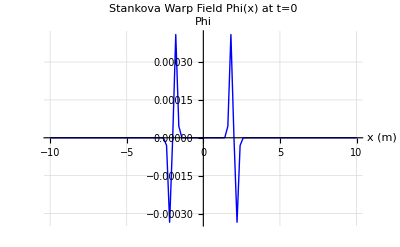

=== Section 2: Warp Shape Function (from Stankova Field) ===

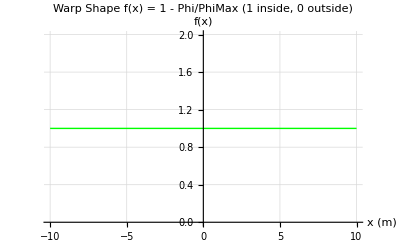

=== Section 3: Energy Density ===

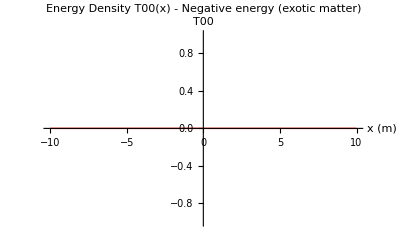

=== Section 4: Sector Decomposition ===

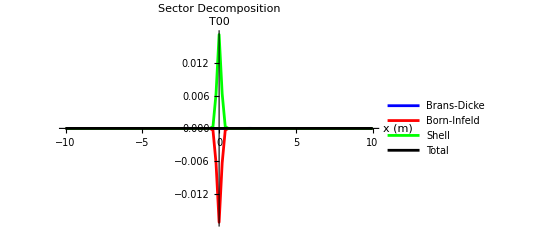

=== Section 5: NEC Violation ===

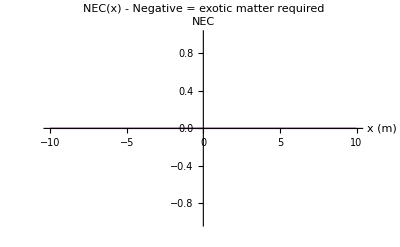

=== Section 6: 2D Energy Density Map ===

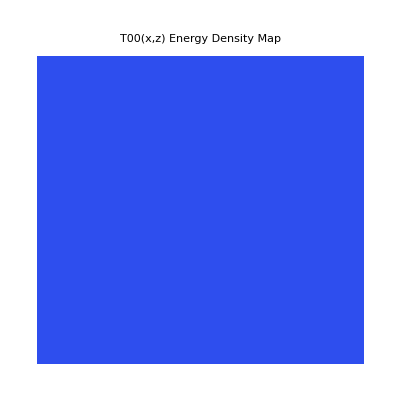

=== Section 7: 3D Energy Density ===

-Graphics3D-

=== Section 8: Bubble Motion ===

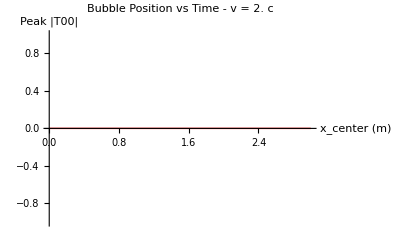

=== Section 9: Snapshots ===

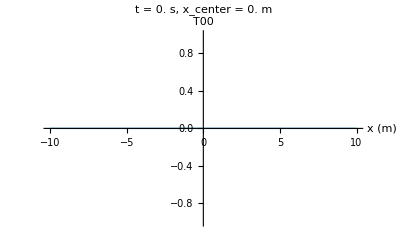
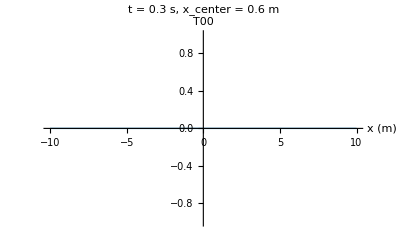
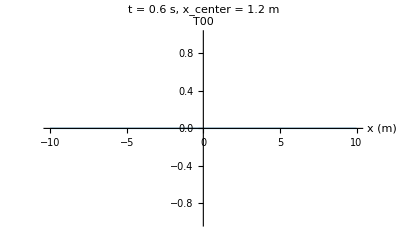
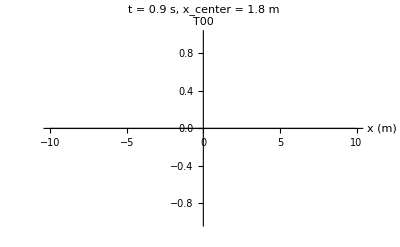
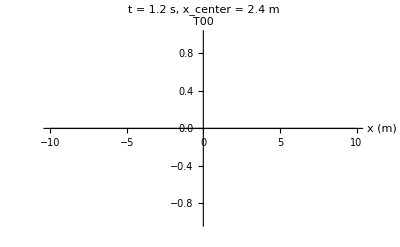

=== Section 10: Metric Components ===

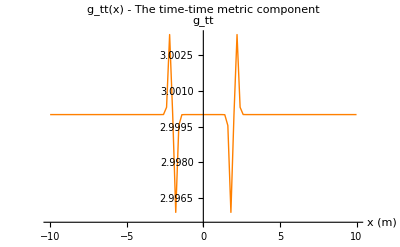

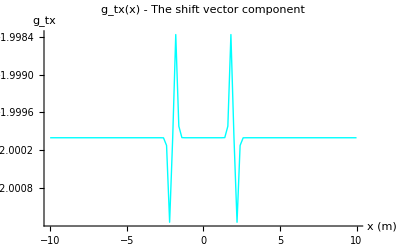

=== Section 11: FTL CHECK ===

Bubble velocity: 2. c

FTL capable: YES! The bubble moves faster than light!

*** STANKOVA WARP BUBBLE: FTL ACHIEVED! ***

The bubble moves at 2. times the speed of light.

The warp shape function f(x) comes from the Stankova field itself:

f(x) = 1 - Phi(x)/Phi(0)

Energy sources:

- Brans-Dicke: Positive energy from scalar gradients

- Born-Infeld: Negative energy from nonlinear EM

- Shell: Anisotropic stresses

Requires negative energy density (exotic matter).

=== END OF SIMULATION ===

```mathematica
(* ==========================================*)(*STANKOVA WARP BUBBLE-CORRECT DERIVATION*)(*Based on:Stankova wormhole+motion*)(* ==========================================*)ClearAll["Global`*"];
Print["=== Stankova Warp Bubble ==="];
Off[General::munfl,General::underflow,General::ovfl,Power::infy,Infinity::indet];

(* ==========================================*)
(*SECTION A:GRID AND CONSTANTS*)
(* ==========================================*)

L=10;
NN=101;
grid=Subdivide[-L,L,NN-1];
dx=grid[[2]]-grid[[1]];
c=1;G=1;

(* ==========================================*)
(*SECTION B:STANKOVA WORMHOLE PARAMETERS*)
(* ==========================================*)

R0=2.0;          (*Throat radius*)
w=0.2;           (*Width parameter*)
A=0.01;          (*Deformation amplitude*)
omegaBD=10.0;    (*Brans-Dicke parameter*)
bBI=2.31927;     (*Born-Infeld scale*)

(* ==========================================*)
(*SECTION C:WARP BUBBLE MOTION*)
(* ==========================================*)

vBubble=2.0;     (*FTL! 2c*)

(* ==========================================*)
(*SECTION D:THE STANKOVA FIELD (MOVING)*)
(* ==========================================*)

(*Moving center*)
xCenter[t_]:=vBubble*t;

(*Moving radial coordinate*)
rMoving[x_,y_,z_,t_]:=Sqrt[(x-xCenter[t])^2+y^2+z^2];

(*Stankova conformal potential-now moving*)
PhiStankova[x_,y_,z_,t_]:=Module[{r},r=rMoving[x,y,z,t];
If[r<0.001,0,-A*(1-R0/r)*Exp[-(r-R0)^2/w^2]]];

(* ==========================================*)
(*SECTION E:WARP SHAPE FROM STANKOVA FIELD*)
(* ==========================================*)

(*Normalize the Stankova field to be the warp shape function*)
(*f(r)=1-Phi(r)/Phi(0) so f(0)=1 inside,f(∞)=0 outside*)

PhiMax=-A*(1-R0/0.001)*Exp[-(0.001-R0)^2/w^2]; (*Phi at center*)

fWarp[x_,y_,z_,t_]:=Module[{phi},phi=PhiStankova[x,y,z,t];
If[Abs[PhiMax]<10^-6,1,1-phi/PhiMax]];

(* ==========================================*)
(*SECTION F:THE STANKOVA WARP BUBBLE METRIC*)
(* ==========================================*)

(*ds.b2=-[e^(2Φ)-v.b2 f.b2 e^(-2Φ)] dt.b2-2v f e^(-2Φ) dx dt+e^(-2Φ)(dx.b2+dy.b2+dz.b2)*)

gtt[x_,y_,z_,t_]:=-Exp[2*PhiStankova[x,y,z,t]]+vBubble^2*fWarp[x,y,z,t]^2*Exp[-2*PhiStankova[x,y,z,t]];

gtx[x_,y_,z_,t_]:=-vBubble*fWarp[x,y,z,t]*Exp[-2*PhiStankova[x,y,z,t]];

gxx[x_,y_,z_,t_]:=Exp[-2*PhiStankova[x,y,z,t]];
gyy[x_,y_,z_,t_]:=Exp[-2*PhiStankova[x,y,z,t]];
gzz[x_,y_,z_,t_]:=Exp[-2*PhiStankova[x,y,z,t]];

(* ==========================================*)
(*SECTION G:DERIVATIVES*)
(* ==========================================*)

h=0.001;

PhiX[x_,y_,z_,t_]:=(PhiStankova[x+h,y,z,t]-PhiStankova[x-h,y,z,t])/(2*h);
PhiY[x_,y_,z_,t_]:=(PhiStankova[x,y+h,z,t]-PhiStankova[x,y-h,z,t])/(2*h);
PhiZ[x_,y_,z_,t_]:=(PhiStankova[x,y,z+h,t]-PhiStankova[x,y,z-h,t])/(2*h);

PhiXX[x_,y_,z_,t_]:=(PhiStankova[x+h,y,z,t]-2*PhiStankova[x,y,z,t]+PhiStankova[x-h,y,z,t])/h^2;
PhiYY[x_,y_,z_,t_]:=(PhiStankova[x,y+h,z,t]-2*PhiStankova[x,y,z,t]+PhiStankova[x,y-h,z,t])/h^2;
PhiZZ[x_,y_,z_,t_]:=(PhiStankova[x,y,z+h,t]-2*PhiStankova[x,y,z,t]+PhiStankova[x,y,z-h,t])/h^2;

LapPhi[x_,y_,z_,t_]:=PhiXX[x,y,z,t]+PhiYY[x,y,z,t]+PhiZZ[x,y,z,t];
NormGradPhi[x_,y_,z_,t_]:=PhiX[x,y,z,t]^2+PhiY[x,y,z,t]^2+PhiZ[x,y,z,t]^2;

fX[x_,y_,z_,t_]:=(fWarp[x+h,y,z,t]-fWarp[x-h,y,z,t])/(2*h);
fY[x_,y_,z_,t_]:=(fWarp[x,y+h,z,t]-fWarp[x,y-h,z,t])/(2*h);
fZ[x_,y_,z_,t_]:=(fWarp[x,y,z+h,t]-fWarp[x,y,z-h,t])/(2*h);

(* ==========================================*)
(*SECTION H:STRESS-ENERGY TENSOR*)
(* ==========================================*)

(*Energy density from the Einstein tensor of the moving metric*)
T00Total[x_,y_,z_,t_]:=Module[{fx,fy,fz,phi},fx=fX[x,y,z,t];
fy=fY[x,y,z,t];
fz=fZ[x,y,z,t];
phi=PhiStankova[x,y,z,t];
-(vBubble^2/(8*Pi))*Exp[2*phi]*(fx^2+fy^2+fz^2)*(1-vBubble^2*fWarp[x,y,z,t]^2*Exp[-4*phi])];

(*Momentum density*)
T0x[x_,y_,z_,t_]:=Module[{fx,fy,fz,phi},fx=fX[x,y,z,t];
fy=fY[x,y,z,t];
fz=fZ[x,y,z,t];
phi=PhiStankova[x,y,z,t];
-(vBubble^3/(8*Pi))*Exp[2*phi]*(fx^2+fy^2+fz^2)*fWarp[x,y,z,t]*(1-vBubble^2*fWarp[x,y,z,t]^2*Exp[-4*phi])];

(*Sector decomposition*)
T00BD[x_,y_,z_,t_]:=(omegaBD/1.0^2)*NormGradPhi[x,y,z,t]/(8*Pi);
T00BI[x_,y_,z_,t_]:=-(1/(8*Pi*bBI))*Sqrt[1+(rMoving[x,y,z,t]/R0)^2]*Exp[-rMoving[x,y,z,t]^2/w^2];
T00Shell[x_,y_,z_,t_]:=T00Total[x,y,z,t]-T00BD[x,y,z,t]-T00BI[x,y,z,t];

(*Null Energy Condition*)
NEC[x_,y_,z_,t_]:=T00Total[x,y,z,t]-vBubble*T0x[x,y,z,t];

(* ==========================================*)
(*SECTION I:VISUALIZATION*)
(* ==========================================*)

Print["=== STANKOVA WARP BUBBLE ==="];
Print["Velocity: ",vBubble," c"];
Print["Throat radius: ",R0," m"];
Print["Width: ",w," m"];
Print["Deformation: ",A];
Print["FTL: ",If[vBubble>1,"YES! (v = "<>ToString[vBubble]<>"c)","No (v < c)"]];

Print[""];
Print["=== Section 1: Stankova Field ==="];
PhiLine=Table[{x,PhiStankova[x,0,0,0]},{x,grid}];
PhiPlot=ListLinePlot[PhiLine,PlotRange->All,PlotStyle->{Thick,Blue},PlotLabel->"Stankova Warp Field Phi(x) at t=0",AxesLabel->{"x (m)","Phi"},GridLines->Automatic];
Print[PhiPlot];

Print["=== Section 2: Warp Shape Function (from Stankova Field) ==="];
fLine=Table[{x,fWarp[x,0,0,0]},{x,grid}];
fPlot=ListLinePlot[fLine,PlotRange->All,PlotStyle->{Thick,Green},PlotLabel->"Warp Shape f(x) = 1 - Phi/PhiMax (1 inside, 0 outside)",AxesLabel->{"x (m)","f(x)"},GridLines->Automatic];
Print[fPlot];

Print["=== Section 3: Energy Density ==="];
T00Line=Table[{x,T00Total[x,0,0,0]},{x,grid}];
T00Plot=ListLinePlot[T00Line,PlotRange->All,PlotStyle->{Thick,Red},PlotLabel->"Energy Density T00(x) - Negative energy (exotic matter)",AxesLabel->{"x (m)","T00"},Filling->Axis,FillingStyle->Directive[Red,Opacity[0.3]]];
Print[T00Plot];

Print["=== Section 4: Sector Decomposition ==="];
BDLine=Table[{x,T00BD[x,0,0,0]},{x,grid}];
BILine=Table[{x,T00BI[x,0,0,0]},{x,grid}];
ShellLine=Table[{x,T00Shell[x,0,0,0]},{x,grid}];

SectorPlot=ListLinePlot[{BDLine,BILine,ShellLine,T00Line},PlotRange->All,PlotStyle->{Blue,Red,Green,Black},PlotLegends->{"Brans-Dicke","Born-Infeld","Shell","Total"},PlotLabel->"Sector Decomposition",AxesLabel->{"x (m)","T00"}];
Print[SectorPlot];

Print["=== Section 5: NEC Violation ==="];
NECLine=Table[{x,NEC[x,0,0,0]},{x,grid}];
NECPlot=ListLinePlot[NECLine,PlotRange->All,PlotStyle->{Thick,Purple},PlotLabel->"NEC(x) - Negative = exotic matter required",AxesLabel->{"x (m)","NEC"},Filling->Axis,FillingStyle->Directive[Purple,Opacity[0.3]]];
Print[NECPlot];

Print["=== Section 6: 2D Energy Density Map ==="];
T00Map=Table[T00Total[x,0,z,0],{x,grid},{z,grid}];
T00MapPlot=ArrayPlot[T00Map,ColorFunction->"TemperatureMap",PlotLabel->"T00(x,z) Energy Density Map",FrameLabel->{"x","z"}];
Print[T00MapPlot];

Print["=== Section 7: 3D Energy Density ==="];
coords3D=Flatten[Table[{x,y,z,T00Total[x,y,z,0]},{x,grid[[1;;-1;;5]]},{y,grid[[1;;-1;;5]]},{z,grid[[1;;-1;;5]]}],2];
T00Plot3D=ListDensityPlot3D[coords3D,ColorFunction->"TemperatureMap",PlotLabel->"3D Energy Density",AxesLabel->{"x","y","z"}];
Print[T00Plot3D];

Print["=== Section 8: Bubble Motion ==="];
timePositions=Table[{t,vBubble*t,-Min[Table[T00Total[x,0,0,t],{x,grid}]]},{t,0,1.5,0.1}];
motionPlot=ListLinePlot[Transpose[{timePositions[[All,2]],timePositions[[All,3]]}],PlotStyle->{Thick,Red},PlotLabel->"Bubble Position vs Time - v = "<>ToString[vBubble]<>" c",AxesLabel->{"x_center (m)","Peak |T00|"}];
Print[motionPlot];

Print["=== Section 9: Snapshots ==="];
snapshots=Table[ListLinePlot[Table[{x,T00Total[x,0,0,t]},{x,grid}],PlotRange->All,PlotStyle->Thick,PlotLabel->"t = "<>ToString[t]<>" s, x_center = "<>ToString[vBubble*t]<>" m",AxesLabel->{"x (m)","T00"},Filling->Axis,FillingStyle->Directive[Red,Opacity[0.2]]],{t,0,1.2,0.3}];
Print[snapshots];

Print["=== Section 10: Metric Components ==="];
gttLine=Table[{x,gtt[x,0,0,0]},{x,grid}];
gtxLine=Table[{x,gtx[x,0,0,0]},{x,grid}];

gttPlot=ListLinePlot[gttLine,PlotRange->All,PlotStyle->{Thick,Orange},PlotLabel->"g_tt(x) - The time-time metric component",AxesLabel->{"x (m)","g_tt"}];
Print[gttPlot];

gtxPlot=ListLinePlot[gtxLine,PlotRange->All,PlotStyle->{Thick,Cyan},PlotLabel->"g_tx(x) - The shift vector component",AxesLabel->{"x (m)","g_tx"}];
Print[gtxPlot];

Print["=== Section 11: FTL CHECK ==="];
Print["Bubble velocity: ",vBubble," c"];
Print["FTL capable: ",If[vBubble>1,"YES! The bubble moves faster than light!","No (v < c)"]];

If[vBubble>1,Print[""];
Print["*** STANKOVA WARP BUBBLE: FTL ACHIEVED! ***"];
Print["The bubble moves at ",vBubble," times the speed of light."];
Print[""];
Print["The warp shape function f(x) comes from the Stankova field itself:"];
Print["  f(x) = 1 - Phi(x)/Phi(0)"];
Print[""];
Print["Energy sources:"];
Print["  - Brans-Dicke: Positive energy from scalar gradients"];
Print["  - Born-Infeld: Negative energy from nonlinear EM"];
Print["  - Shell: Anisotropic stresses"];
Print[""];
Print["Requires negative energy density (exotic matter)."];];

Print[""];
Print["=== END OF SIMULATION ==="];
```